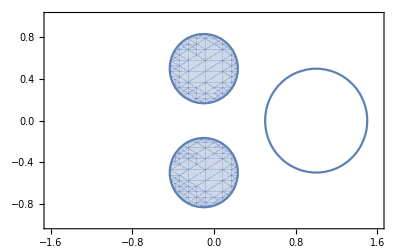

```mathematica
p = (x-1)^2+y^2-1/4;
c1 = (x+0.1)^2+(y-0.5)^2-1/9;
c2= (x+0.1)^2+(y+0.5)^2-1/9;
CP = ContourPlot[p==0,{x,-1.6,1.6},{y,-1,1}];
RP1 = RegionPlot[c1≤ 0,{x,-1.6,1.6},{y,-1,1}];
RP2 = RegionPlot[c2≤ 0,{x,-1.6,1.6},{y,-1,1}];
Show[RP1,RP2,CP,AspectRatio-> 1/1.6]
```

```mathematica
<<ToMatlab`
```

```mathematica
p/.x-> xx/.y-> yy//ToMatlab//TextForm
```

(-1/4)+((-1)+xx).^2+yy.^2;

```mathematica
c1/.x-> xx/.y-> yy//ToMatlab//TextForm
```

(-1/9)+(0.1E0+xx).^2+((-0.5E0)+yy).^2;

```mathematica
c2/.x-> xx/.y-> yy//ToMatlab//TextForm
```

(-1/9)+(0.1E0+xx).^2+(0.5E0+yy).^2;